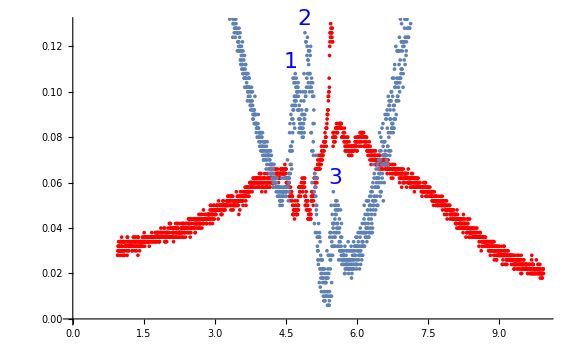

{127.823,17.4937}

{100.5,4.83144}

{114.161,11.1626}

{11.4161,1.44227}

```mathematica
SetDirectory[NotebookDirectory[]];
las=Drop[Drop[Import["../osc/ALL0002/F0002CH1.CSV", {"Data", All, {4,5}}], -13],237];
pd = Drop[Drop[Import["../osc/ALL0002/F0002CH2.CSV",{"Data",All,{4,5}}],237], -13];
Show[ListPlot[Map[{#[[1]],#[[2]]*5-0.0388*5+0.2}&,pd],PlotStyle->Red],ListPlot[Map[{#[[1]],#[[2]]-1.17+0.2 }&,las]],Graphics[Text[Style["1",FontSize->22,FontColor->Blue],{4.6,0.113}]],Graphics[Text[Style["2",FontSize->22,FontColor->Blue],{4.9,0.132}]],Graphics[Text[Style["3",FontSize->22,FontColor->Blue],{5.55,0.062}]],Graphics[Text[Style["MOT",FontSize->18,FontColor->Red],{5.6,0.1345}]],Axes -> {True, False},ImageSize->Large]
p1 = {4.708,0.024};
p2 = {4.956, 0.024};
p3 = {5.556, 0.016};
d12 = 31.7;
d23 = 60.3;
C12 = {(p2[[1]]-p1[[1]])/d12, Sqrt[p2[[2]]^2 + p1[[2]]^2]/d12 };
C23 = {(p3[[1]]-p2[[1]])/d23, Sqrt[p3[[2]]^2 + p2[[2]]^2]/d23 };
Cinv12 = {1/C12[[1]],1/C12[[1]]^2 * C12[[2]]}
Cinv23 = {1/C23[[1]],1/C23[[1]]^2 * C23[[2]]}
CinvAvg = {Mean[{Cinv12[[1]],Cinv23[[1]]}],Mean[{Cinv12[[2]],Cinv23[[2]]}]}
mot = {0.1, 0.008};
Δ = {mot[[1]]*CinvAvg[[1]],Sqrt[mot[[1]]^2*CinvAvg[[2]]^2 + CinvAvg[[1]]^2*mot[[2]]^2]}
```

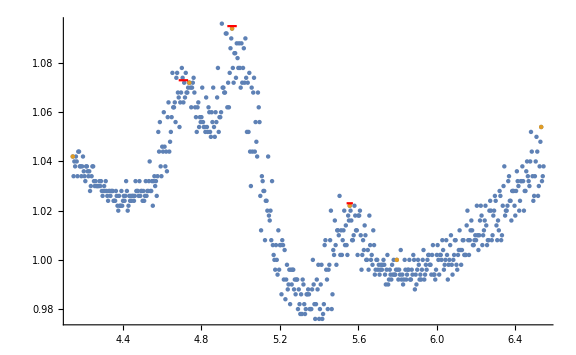

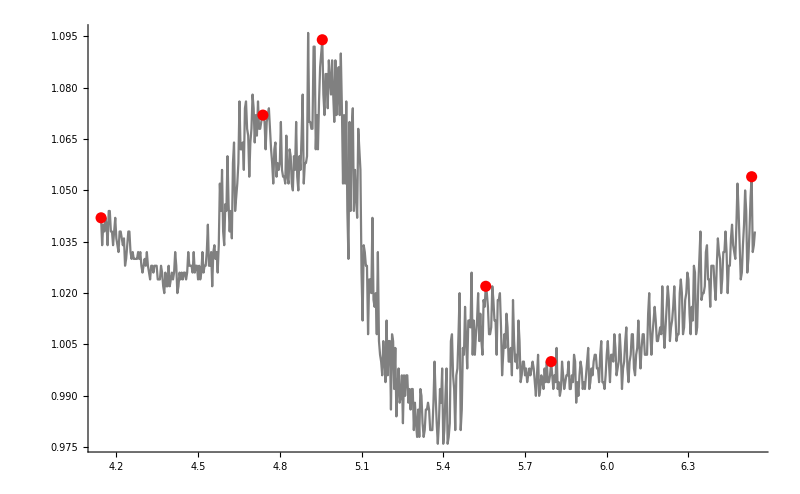

{4.738,4.956,5.556}

```mathematica
las=Drop[Drop[Import["../osc/ALL0002/F0002CH1.CSV", {"Data", All, {4,5}}], -13],237];
t = TimeSeries[las[[800;;1400]]];
Show[ListPlot[{t,FindPeaks[t,5.5]}],Plot[1.073,{x,4.708-0.024, 4.708+0.024},PlotStyle->Red],Plot[1.095,{x, 4.956-0.024,4.956+0.024},PlotStyle->Red],Plot[1.023,{x, 5.556-0.016,5.556+0.016},PlotStyle->Red],ImageSize->Large]
Show[{ListLinePlot[t,PlotStyle->Gray],ListPlot[FindPeaks[t,5.5],PlotStyle->{Red,PointSize->0.01}]},ImageSize->800]
FindPeaks[t,5.5]["PathTimes"][[2;;4]]
```

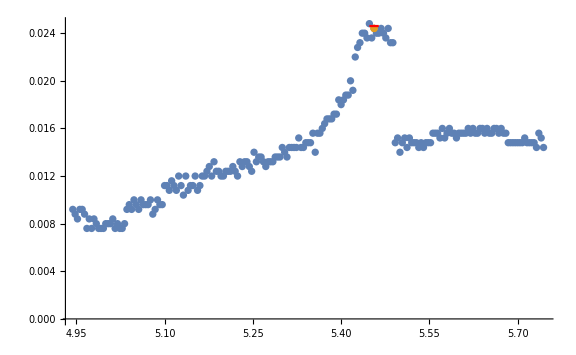

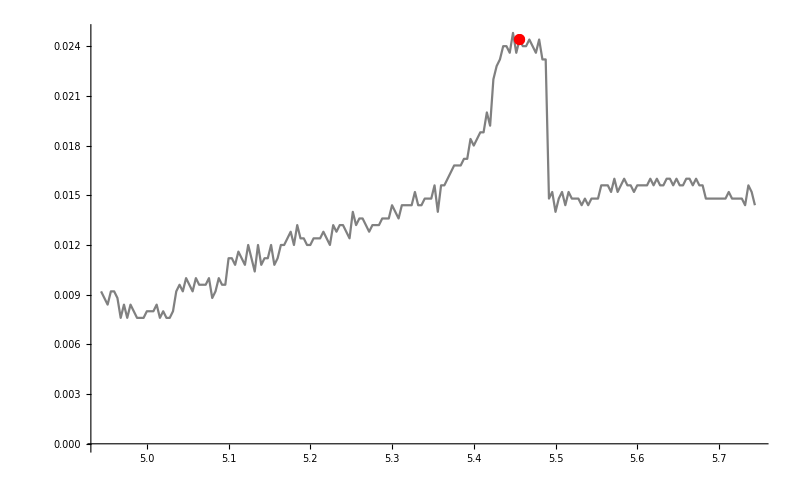

{5.456}

```mathematica
pd = Drop[Drop[Import["../osc/ALL0002/F0002CH2.CSV",{"Data",All,{4,5}}],237], -13];
ts = TimeSeries[pd[[1000;;1200]]];
Show[ListPlot[{ts,FindPeaks[ts,100]}],Plot[0.0246,{x,5.456-0.008,5.456+0.008},PlotStyle->Red],ImageSize->Large]
Show[{ListLinePlot[ts,PlotStyle->Gray],ListPlot[FindPeaks[ts,100],PlotStyle->{Red,PointSize->0.01}]},ImageSize->800]
FindPeaks[ts,100]["PathTimes"]
```

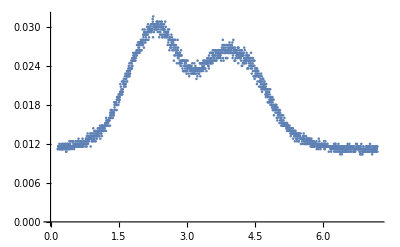

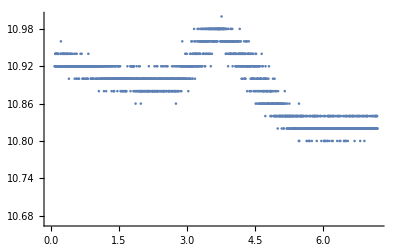

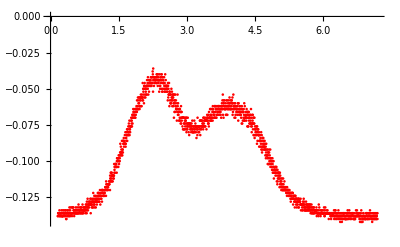

```mathematica
las2=Drop[Import["../osc/ALL0004/F0004CH1.CSV", {"Data", All, {4,5}}],-700];
pd2 = Drop[Drop[Import["../osc/ALL0004/F0004CH2.CSV",{"Data",All,{4,5}}],40],-700];
ListPlot[Map[{#[[1]],#[[2]]}&,pd2]]
ListPlot[Map[{#[[1]],#[[2]] }&,las2]]
Show[ListPlot[Map[{#[[1]],#[[2]]*5-0.0388*5}&,pd2],PlotStyle->Red],ListPlot[Map[{#[[1]],#[[2]]-1.17 }&,las2]]]
```